# Investigate finding maxima for peak detection

## Set up the basic functions

f is the Lorentzian function/Cauchy PDF as defined in Paul Anderson's thesis.  This makes γ the width at half-height, amp the amplitude of the mode, and x0 the location of the mode on the x axis.

```mathematica
f[x_,amp_,γ_,x0_]:=amp γ^2/(4(x-x0)^2+γ^2)
```

And it is, plotted on a graph

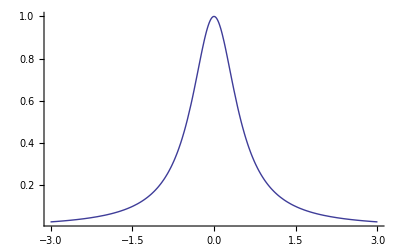

```mathematica
Plot[{f[x,1,1,0]},{x,-3,3},PlotRange->All,AxesOrigin->{0,0}]
```

## How does maximum finding work as a peak-detector?

### Performance for one function

One function is a single peak located at x0

```mathematica
oneFunction[y_,x0_]:=Evaluate[f[x,1,1,x0]]
```

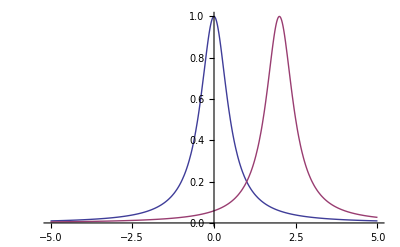

```mathematica
Plot[{oneFunction[x,0],oneFunction[x,2]},{x,-5,5},PlotRange->All]
```

This (expectedly) always has its maximum at x0.

```mathematica
Module[{q},q[x_]:=oneFunction[x,x0];Reduce[D[q[x],x]==0&&D[q[x],{x,2}]<0,Reals]]
```

x==x0

### Performance for two functions of equal width and height

twoFunctions defines two identical peaks.  One peak is at -x0 and the other at x0.  So the distance between them is 2 x0.

```mathematica
twoFunctions[y_,x0_]:=Evaluate[f[y,1,1,-x0]+f[y,1,1,x0]]
```

Both locations are maxima only when x0 ==0

```mathematica
Module[{q},q[x_]:=twoFunctions[x,x0];
With[{firstD=D[twoFunctions[x,x0],x],secD=D[twoFunctions[x,x0],{x,2}]},
With[{firstDAtNegX0=firstD/.x->-x0,firstDAtX0=firstD/.x->x0,
secDAtNegX0=secD/.x->-x0,secDAtX0=secD/.x->x0},
Reduce[firstDAtNegX0==0&&firstDAtX0==0&&secDAtNegX0<0&&secDAtX0<0,Reals]
]]]
```

x0==0

Due to symmetry of the original and filter functions, the maxima must be located symmetrically.  Now, where are the positive maxima?

```mathematica
Module[{q},q[x_]:=twoFunctions[x,x0];
With[{firstD=D[twoFunctions[x,x0],x],secD=D[twoFunctions[x,x0],{x,2}]},
Reduce[firstD==0&&secD<0&&x0>=0&&x>=0,Reals]
]]
```

(0≤x0<1/(2 √3)&&x==0)||(x0>1/(2 √3)&&x==Root[1-8 x0^2-48 x0^4+(8+32 x0^2) #1^2+16 #1^4&,2])

Here there are never more than two maxima.  When |x0|<1/(2 √3) the two maxima are indistinguishable and the peak is located at 0.  Thus the peaks are indistinguishable when separated by less than 0.57735 units. Otherwise they are located at x==Root[1-8 x0^2-48 x0^4+(8+32 x0^2) #1^2+16 #1^4&,2]

#### Errors in peak position

twoFuncX gives the x position of the largest maximum for a given x0

```mathematica
twoFuncX[x0_]:=Which[0≤Abs[x0]<1/(2 √3),0,
True,Root[1-8 x0^2-48 x0^4+(8+32 x0^2) #1^2+16 #1^4&,2]
]
```

The error function grows seadily until the located maximum finally splits into two.  Then it decreases gradually, eventually reaching 0 asymptotically.

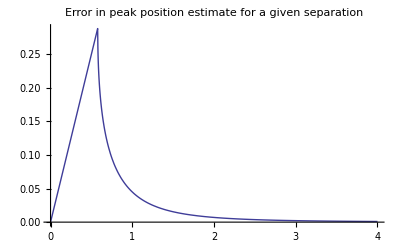

```mathematica
Plot[sep/2-twoFuncX[sep/2],{sep,0,4},PlotRange->All,PlotLabel->"Error in peak position estimate for a given separation",FrameLabel->{"Peak separation","Distance of predicted from actual peak"},AxesOrigin->{0,0}]
```

When expressed as a percentage of the distance of the peak from the center, the error looks slightly different.

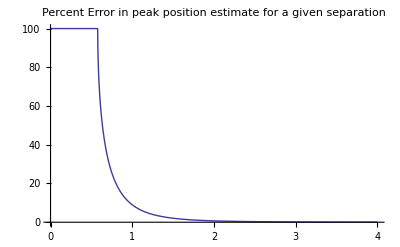

```mathematica
Plot[100*(sep/2-twoFuncX[sep/2])/(sep/2),{sep,0,4},PlotRange->All,PlotLabel->"Percent Error\nin peak position estimate for a given separation",FrameLabel->{"Peak separation","Distance of predicted from actual peak"},AxesOrigin->{0,0}]
```

The maximum % error when they are separated by more than 1 unit is: 8.98% when they are separated by 1 units.

```mathematica
NMaximize[{Abs[(sep/2-twoFuncX[sep/2])/(sep/2)],sep>1},{sep}]
```

{0.0898203,{sep→1.}}

### Performance for two functions of equal width but different heights

Here we have two functions of different height, symmetrically located.  The one at x0 is amp units high and the one at x0 is 1 unit high

```mathematica
twoFunctionsDH[y_,x0_,amp_]:=Evaluate[f[y,1,1,-x0]+f[y,amp,1,x0]]
```

Again, they only correspond exactly when x0==0

```mathematica
Module[{q},q[x_]:=twoFunctionsDH[x,x0,amp];
With[{firstD=D[q[x],x],secD=D[q[x],{x,2}]},
With[{firstDAtNegX0=firstD/.x->-x0,firstDAtX0=firstD/.x->x0,
secDAtNegX0=secD/.x->-x0,secDAtX0=secD/.x->x0},
Reduce[amp>1&&firstDAtNegX0==0&&firstDAtX0==0&&secDAtNegX0<0&&secDAtX0<0,Reals]
]]]
```

amp>1&&x0==0

Location of the maxima:

```mathematica
Module[{q},q[x_]:=twoFunctionsDH[x,x0,amp];
With[{firstD=D[q[x],x],secD=D[q[x],{x,2}]},
Reduce[firstD==0&&secD<0&&x0>=0&&amp>=1,{x},Reals]
]]
```

(0≤x0<1/(2 √3)&&amp≥1&&x==Root[x0-amp x0+8 x0^3-8 amp x0^3+16 x0^5-16 amp x0^5+(1+amp-8 x0^2-8 amp x0^2-48 x0^4-48 amp x0^4) #1+(-8 x0+8 amp x0+32 x0^3-32 amp x0^3) #1^2+(8+8 amp+32 x0^2+32 amp x0^2) #1^3+(-48 x0+48 amp x0) #1^4+(16+16 amp) #1^5&,1])||(x0==1/(2 √3)&&amp>1&&x==Root[x0-amp x0+8 x0^3-8 amp x0^3+16 x0^5-16 amp x0^5+(1+amp-8 x0^2-8 amp x0^2-48 x0^4-48 amp x0^4) #1+(-8 x0+8 amp x0+32 x0^3-32 amp x0^3) #1^2+(8+8 amp+32 x0^2+32 amp x0^2) #1^3+(-48 x0+48 amp x0) #1^4+(16+16 amp) #1^5&,1])||(x0>1/(2 √3)&&((1≤amp<Root[1+48 x0^2+768 x0^4+4096 x0^6+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1+(6-288 x0^2-4608 x0^4-21504 x0^6-184320 x0^8-884736 x0^10-1769472 x0^12) #1^2+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1^3+(1+48 x0^2+768 x0^4+4096 x0^6) #1^4&,4]&&(x==Root[x0-amp x0+8 x0^3-8 amp x0^3+16 x0^5-16 amp x0^5+(1+amp-8 x0^2-8 amp x0^2-48 x0^4-48 amp x0^4) #1+(-8 x0+8 amp x0+32 x0^3-32 amp x0^3) #1^2+(8+8 amp+32 x0^2+32 amp x0^2) #1^3+(-48 x0+48 amp x0) #1^4+(16+16 amp) #1^5&,1]||x==Root[x0-amp x0+8 x0^3-8 amp x0^3+16 x0^5-16 amp x0^5+(1+amp-8 x0^2-8 amp x0^2-48 x0^4-48 amp x0^4) #1+(-8 x0+8 amp x0+32 x0^3-32 amp x0^3) #1^2+(8+8 amp+32 x0^2+32 amp x0^2) #1^3+(-48 x0+48 amp x0) #1^4+(16+16 amp) #1^5&,3]))||(amp==Root[1+48 x0^2+768 x0^4+4096 x0^6+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1+(6-288 x0^2-4608 x0^4-21504 x0^6-184320 x0^8-884736 x0^10-1769472 x0^12) #1^2+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1^3+(1+48 x0^2+768 x0^4+4096 x0^6) #1^4&,4]&&x==Root[x0-amp x0+8 x0^3-8 amp x0^3+16 x0^5-16 amp x0^5+(1+amp-8 x0^2-8 amp x0^2-48 x0^4-48 amp x0^4) #1+(-8 x0+8 amp x0+32 x0^3-32 amp x0^3) #1^2+(8+8 amp+32 x0^2+32 amp x0^2) #1^3+(-48 x0+48 amp x0) #1^4+(16+16 amp) #1^5&,3])||(amp>Root[1+48 x0^2+768 x0^4+4096 x0^6+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1+(6-288 x0^2-4608 x0^4-21504 x0^6-184320 x0^8-884736 x0^10-1769472 x0^12) #1^2+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1^3+(1+48 x0^2+768 x0^4+4096 x0^6) #1^4&,4]&&x==Root[x0-amp x0+8 x0^3-8 amp x0^3+16 x0^5-16 amp x0^5+(1+amp-8 x0^2-8 amp x0^2-48 x0^4-48 amp x0^4) #1+(-8 x0+8 amp x0+32 x0^3-32 amp x0^3) #1^2+(8+8 amp+32 x0^2+32 amp x0^2) #1^3+(-48 x0+48 amp x0) #1^4+(16+16 amp) #1^5&,1])))

```mathematica
twoFunctionDHMaxes[x0_,amp_]:=Which[
0≤x0<1/(2 √3)&&amp≥1,{Root[x0-amp x0+8 x0^3-8 amp x0^3+16 x0^5-16 amp x0^5+(1+amp-8 x0^2-8 amp x0^2-48 x0^4-48 amp x0^4) #1+(-8 x0+8 amp x0+32 x0^3-32 amp x0^3) #1^2+(8+8 amp+32 x0^2+32 amp x0^2) #1^3+(-48 x0+48 amp x0) #1^4+(16+16 amp) #1^5&,1]},
x0==1/(2 √3)&&amp>1,{Root[x0-amp x0+8 x0^3-8 amp x0^3+16 x0^5-16 amp x0^5+(1+amp-8 x0^2-8 amp x0^2-48 x0^4-48 amp x0^4) #1+(-8 x0+8 amp x0+32 x0^3-32 amp x0^3) #1^2+(8+8 amp+32 x0^2+32 amp x0^2) #1^3+(-48 x0+48 amp x0) #1^4+(16+16 amp) #1^5&,1]},
x0>1/(2 √3)&&1≤amp<Root[1+48 x0^2+768 x0^4+4096 x0^6+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1+(6-288 x0^2-4608 x0^4-21504 x0^6-184320 x0^8-884736 x0^10-1769472 x0^12) #1^2+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1^3+(1+48 x0^2+768 x0^4+4096 x0^6) #1^4&,4],
{Root[x0-amp x0+8 x0^3-8 amp x0^3+16 x0^5-16 amp x0^5+(1+amp-8 x0^2-8 amp x0^2-48 x0^4-48 amp x0^4) #1+(-8 x0+8 amp x0+32 x0^3-32 amp x0^3) #1^2+(8+8 amp+32 x0^2+32 amp x0^2) #1^3+(-48 x0+48 amp x0) #1^4+(16+16 amp) #1^5&,1],
Root[x0-amp x0+8 x0^3-8 amp x0^3+16 x0^5-16 amp x0^5+(1+amp-8 x0^2-8 amp x0^2-48 x0^4-48 amp x0^4) #1+(-8 x0+8 amp x0+32 x0^3-32 amp x0^3) #1^2+(8+8 amp+32 x0^2+32 amp x0^2) #1^3+(-48 x0+48 amp x0) #1^4+(16+16 amp) #1^5&,3]},x0>1/(2 √3)&&amp==Root[1+48 x0^2+768 x0^4+4096 x0^6+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1+(6-288 x0^2-4608 x0^4-21504 x0^6-184320 x0^8-884736 x0^10-1769472 x0^12) #1^2+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1^3+(1+48 x0^2+768 x0^4+4096 x0^6) #1^4&,4],
{Root[x0-amp x0+8 x0^3-8 amp x0^3+16 x0^5-16 amp x0^5+(1+amp-8 x0^2-8 amp x0^2-48 x0^4-48 amp x0^4) #1+(-8 x0+8 amp x0+32 x0^3-32 amp x0^3) #1^2+(8+8 amp+32 x0^2+32 amp x0^2) #1^3+(-48 x0+48 amp x0) #1^4+(16+16 amp) #1^5&,3]},
x0>1/(2 √3)&&amp>Root[1+48 x0^2+768 x0^4+4096 x0^6+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1+(6-288 x0^2-4608 x0^4-21504 x0^6-184320 x0^8-884736 x0^10-1769472 x0^12) #1^2+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1^3+(1+48 x0^2+768 x0^4+4096 x0^6) #1^4&,4],{Root[x0-amp x0+8 x0^3-8 amp x0^3+16 x0^5-16 amp x0^5+(1+amp-8 x0^2-8 amp x0^2-48 x0^4-48 amp x0^4) #1+(-8 x0+8 amp x0+32 x0^3-32 amp x0^3) #1^2+(8+8 amp+32 x0^2+32 amp x0^2) #1^3+(-48 x0+48 amp x0) #1^4+(16+16 amp) #1^5&,1]},
True,Print["Bad value passed to twoFunctionDHMaxes x0:"~~ToString[x0]~~" amp:"~~ToString[amp]];{0}
]
```

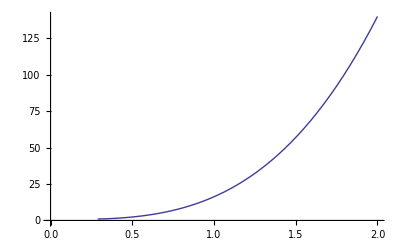

```mathematica
Plot[Root[1+48 x0^2+768 x0^4+4096 x0^6+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1+(6-288 x0^2-4608 x0^4-21504 x0^6-184320 x0^8-884736 x0^10-1769472 x0^12) #1^2+(4-96 x0^2+1920 x0^4+20992 x0^6+73728 x0^8) #1^3+(1+48 x0^2+768 x0^4+4096 x0^6) #1^4&,4],{x0,0,2}]
```

```mathematica
Plot3D[Log[x0-Max[twoFunctionDHMaxes[x0,amp]]],{x0,0,2},{amp,1,100},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Log[Min[twoFunctionDHMaxes[x0,amp]]+x0],{x0,0,2},{amp,1,100},PlotRange->All]
```

-Graphics3D-

```mathematica
twoFunctionDHMaxes[0.4,3.]
```

0.377741